```mathematica
(* Filename: Errors_By_w2_revA_SRCK2_avr_Al_DN
*)
(* Ver. 0 (28-Aug-2025) *)
(*
This file is a program code in Mathematica to get a plot about errors in Fig. 2.
*)
```

```mathematica
nn=127;
```

```mathematica
(***** In the following line, you need to set a path 
to the folder "For_figs_1_2". *****)
(*
datadir= "D:/.../For_figs_1_2/";
*)
```

```mathematica
mydirA80 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_4/St80_Se16_Tr1000_B256"];
(***)
mydirA53 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_8/St53_Se16_Tr1000_B256"];
(***)
mydirA38 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_16/St38_Se16_Tr1000_B256"];
(***)
mydirA28 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_32/St28_Se16_Tr1000_B256"];
(***)
mydirA19 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_64/St19_Se16_Tr1000_B256"];
(***)
mydirA14 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_128/St14_Se16_Tr1000_B256"];
```

```mathematica
fdim=2;
numSetForPrecise=16;
```

```mathematica
numSetForData=16;
```

```mathematica
(* For precise solutions *)
dataMomA14ForEachY=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomA14ForEachY[[ii]]=Table[{},{ii,1,nn}];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirA14<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA14ForEachY[[ii]][[kk]]=locTmp[[kk]];
];
For[iiset = 2,iiset≤numSetForPrecise,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirA14<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA14ForEachY[[ii]][[kk]]+=locTmp[[kk]];
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomA14ForEachY[[ii]][[kk]]/=numSetForPrecise;

];
];(* End of for ii *)
```

```mathematica
dataMomA80ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomA80ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomA80ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomA80ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomA80ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirA80<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA80ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirA80<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA80ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomA80ForEachYAllSet[[ii]][[kk]]=dataMomA80ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomA80ForEachYAllSet[[ii]][[kk]]+=dataMomA80ForEachYEachSet[[ii,kk,iiset]];
];
dataMomA80ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
(***)
dataMomA53ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomA53ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomA53ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomA53ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomA53ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirA53<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA53ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirA53<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA53ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomA53ForEachYAllSet[[ii]][[kk]]=dataMomA53ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomA53ForEachYAllSet[[ii]][[kk]]+=dataMomA53ForEachYEachSet[[ii,kk,iiset]];
];
dataMomA53ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
(***)
dataMomA38ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomA38ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomA38ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomA38ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomA38ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirA38<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA38ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirA38<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA38ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomA38ForEachYAllSet[[ii]][[kk]]=dataMomA38ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomA38ForEachYAllSet[[ii]][[kk]]+=dataMomA38ForEachYEachSet[[ii,kk,iiset]];
];
dataMomA38ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
(***)
dataMomA28ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomA28ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomA28ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomA28ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomA28ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirA28<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA28ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirA28<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA28ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomA28ForEachYAllSet[[ii]][[kk]]=dataMomA28ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomA28ForEachYAllSet[[ii]][[kk]]+=dataMomA28ForEachYEachSet[[ii,kk,iiset]];
];
dataMomA28ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
(***)
dataMomA19ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomA19ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomA19ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomA19ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomA19ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirA19<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA19ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirA19<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA19ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomA19ForEachYAllSet[[ii]][[kk]]=dataMomA19ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomA19ForEachYAllSet[[ii]][[kk]]+=dataMomA19ForEachYEachSet[[ii,kk,iiset]];
];
dataMomA19ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
```

```mathematica
preciseMomForEachY=dataMomA14ForEachY;
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomA80=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomA80ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomA80[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomA53=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomA53ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomA53[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomA38=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomA38ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomA38[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomA28=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomA28ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomA28[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomA19=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomA19ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomA19[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
```

```mathematica
difflistMomA=Table[{},{ii,1,fdim}];
tmpMini=Table[{},{ii,1,5}];
For[ii=1, ii≤fdim, ii++,
tmpMini[[1]]={Log[2,1/4],Log[2,errorMomA80[[ii]]]};
tmpMini[[2]]={Log[2,1/8],Log[2,errorMomA53[[ii]]]};
tmpMini[[3]]={Log[2,1/16],Log[2,errorMomA38[[ii]]]};
tmpMini[[4]]={Log[2,1/32],Log[2,errorMomA28[[ii]]]};
tmpMini[[5]]={Log[2,1/64],Log[2,errorMomA19[[ii]]]};
difflistMomA[[ii]]=Table[tmpMini[[ii]],{ii,1,5}];
];
```

```mathematica
plotlistMomA=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
plotlistMomA[[ii]]=ListPlot[difflistMomA[[ii]],Joined->True(*,PlotStyle->Dashing[{0.075,0.05}]*)(*,PlotStyle->PointSize[0.02]*)];
];
```

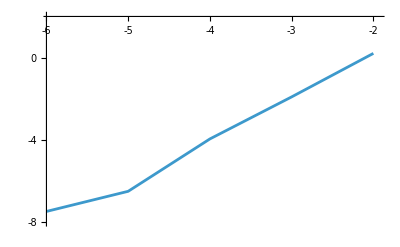

```mathematica
ll=0.015;
ii=1;
Show[plotlistMomA[[ii]],PlotRange->{{-6+0.05,-2+0.05},{-8,2}},AxesOrigin->{-6,2},Ticks->{Table[{-1ii,ToString[-1ii],ll},{ii,2,6}],Table[{-2ii,ToString[-2ii],ll},{ii,-2,6}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```

```mathematica
numSubSetForData=8;(* 1, 2, 4, 8, 16 *)
numMiniSet=numSetForData/numSubSetForData;
(***)
dataMomA80ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomA80ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomA80ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
(*
If[(1==ii)&&(2>=kk),
Print["(ii=",ii,", kk=",kk,"); ","tmpSt=",tmpSt,", tmpEnd=",tmpEnd];
];
*)
dataMomA80ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomA80ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomA80ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomA80ForEachYEachSet[[ii,kk,iiset]];
];
dataMomA80ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
(***)
dataMomA53ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomA53ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomA53ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
dataMomA53ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomA53ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomA53ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomA53ForEachYEachSet[[ii,kk,iiset]];
];
dataMomA53ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
(***)
dataMomA38ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomA38ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomA38ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
dataMomA38ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomA38ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomA38ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomA38ForEachYEachSet[[ii,kk,iiset]];
];
dataMomA38ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
(***)
dataMomA28ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomA28ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomA28ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
dataMomA28ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomA28ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomA28ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomA28ForEachYEachSet[[ii,kk,iiset]];
];
dataMomA28ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
(***)
dataMomA19ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomA19ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomA19ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
dataMomA19ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomA19ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomA19ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomA19ForEachYEachSet[[ii,kk,iiset]];
];
dataMomA19ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
```

```mathematica
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomA80SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomA80SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomA80ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomA80ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomA80SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
(***)
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomA53SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomA53SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomA53ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomA53ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomA53SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
(***)
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomA38SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomA38SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomA38ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomA38ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomA38SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
(***)
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomA28SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomA28SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomA28ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomA28ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomA28SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
(***)
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomA19SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomA19SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomA19ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomA19ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomA19SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
```

```mathematica
errorMomA80Ave=Table[{},{ii,1,fdim}];
errorMomA80Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomA80SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomA80Ave[[ii]]=Mean[tmpErrorList];
errorMomA80Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomA80Ave[[ii]])^2]/numSubSetForData];
];
(***)
errorMomA53Ave=Table[{},{ii,1,fdim}];
errorMomA53Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomA53SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomA53Ave[[ii]]=Mean[tmpErrorList];
errorMomA53Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomA53Ave[[ii]])^2]/numSubSetForData];
];
(***)
errorMomA38Ave=Table[{},{ii,1,fdim}];
errorMomA38Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomA38SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomA38Ave[[ii]]=Mean[tmpErrorList];
errorMomA38Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomA38Ave[[ii]])^2]/numSubSetForData];
];
(***)
errorMomA28Ave=Table[{},{ii,1,fdim}];
errorMomA28Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomA28SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomA28Ave[[ii]]=Mean[tmpErrorList];
errorMomA28Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomA28Ave[[ii]])^2]/numSubSetForData];
];
(***)
errorMomA19Ave=Table[{},{ii,1,fdim}];
errorMomA19Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomA19SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomA19Ave[[ii]]=Mean[tmpErrorList];
errorMomA19Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomA19Ave[[ii]])^2]/numSubSetForData];
];
```

```mathematica
difflistMomAForAve=Table[{},{ii,1,fdim}];
tmpMini=Table[{},{ii,1,5}];
For[ii=1, ii≤fdim, ii++,
tmpMini[[1]]={Log[2,1/4],Log[2,errorMomA80Ave[[ii]]]};
tmpMini[[2]]={Log[2,1/8],Log[2,errorMomA53Ave[[ii]]]};
tmpMini[[3]]={Log[2,1/16],Log[2,errorMomA38Ave[[ii]]]};
tmpMini[[4]]={Log[2,1/32],Log[2,errorMomA28Ave[[ii]]]};
tmpMini[[5]]={Log[2,1/64],Log[2,errorMomA19Ave[[ii]]]};
difflistMomAForAve[[ii]]=Table[tmpMini[[ii]],{ii,1,5}];
];
```

```mathematica
plotlistMomAForAve=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
plotlistMomAForAve[[ii]]=ListPlot[difflistMomAForAve[[ii]],Joined->True(*,PlotStyle->Dashing[{0.075,0.05}]*)(*,PlotStyle->PointSize[0.02]*)];
];
```

```mathematica
plotMiniBarA80ForMom=Table[{},{ii,1,fdim}];
plotMiniBarA53ForMom=Table[{},{ii,1,fdim}];
plotMiniBarA38ForMom=Table[{},{ii,1,fdim}];
plotMiniBarA28ForMom=Table[{},{ii,1,fdim}];
plotMiniBarA19ForMom=Table[{},{ii,1,fdim}];
(***)
For[ii=1, ii≤fdim, ii++,
tmpStep=1/4;
plotMiniBarA80ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomA80Ave[[ii]]+errorMomA80Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomA80Ave[[ii]]-errorMomA80Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarA53ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomA53Ave[[ii]]+errorMomA53Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomA53Ave[[ii]]-errorMomA53Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarA38ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomA38Ave[[ii]]+errorMomA38Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomA38Ave[[ii]]-errorMomA38Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarA28ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomA28Ave[[ii]]+errorMomA28Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomA28Ave[[ii]]-errorMomA28Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarA19ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomA19Ave[[ii]]+errorMomA19Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomA19Ave[[ii]]-errorMomA19Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
];
```

```mathematica
tmpUpperListA=Table[{},{ii,1,fdim}];
tmpLowerListA=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpUpperListA[[ii]]={{Log[2,1/4],Log[2,errorMomA80Ave[[ii]]+errorMomA80Std[[ii]]]},{Log[2,1/8],Log[2,errorMomA53Ave[[ii]]+errorMomA53Std[[ii]]]},{Log[2,1/16],Log[2,errorMomA38Ave[[ii]]+errorMomA38Std[[ii]]]},{Log[2,1/32],Log[2,errorMomA28Ave[[ii]]+errorMomA28Std[[ii]]]},{Log[2,1/64],Log[2,errorMomA19Ave[[ii]]+errorMomA19Std[[ii]]]}};
tmpLowerListA[[ii]]={{Log[2,1/4],Log[2,errorMomA80Ave[[ii]]-errorMomA80Std[[ii]]]},{Log[2,1/8],Log[2,errorMomA53Ave[[ii]]-errorMomA53Std[[ii]]]},{Log[2,1/16],Log[2,errorMomA38Ave[[ii]]-errorMomA38Std[[ii]]]},{Log[2,1/32],Log[2,errorMomA28Ave[[ii]]-errorMomA28Std[[ii]]]},{Log[2,1/64],Log[2,errorMomA19Ave[[ii]]-errorMomA19Std[[ii]]]}};
];
```

```mathematica
plotMarkerListAForMom=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
plotMarkerListAForMom[[ii]]=ListPlot[{tmpUpperListA[[ii]],tmpLowerListA[[ii]]},PlotMarkers->{"",""}(*,PlotMarkers->{"",""}*)];
];
```

numSubSetForData=8

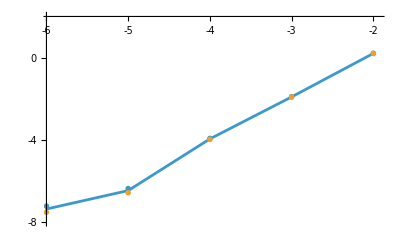

```mathematica
ll=0.03;
Print["numSubSetForData=",numSubSetForData];
ii=1;
Show[plotlistMomAForAve[[ii]],plotMarkerListAForMom[[ii]],plotMiniBarA80ForMom[[ii]],plotMiniBarA53ForMom[[ii]],plotMiniBarA38ForMom[[ii]],plotMiniBarA28ForMom[[ii]],plotMiniBarA19ForMom[[ii]],PlotRange->{{-6+0.05,-2+0.05},{-8,2}},AxesOrigin->{-6,2},Ticks->{Table[{-1ii,ToString[-1ii],ll},{ii,2,6}],Table[{-2ii,ToString[-2ii],ll},{ii,-2,6}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```